```mathematica
观察轨道坐标的时间变化
```

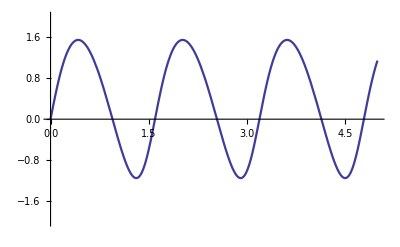

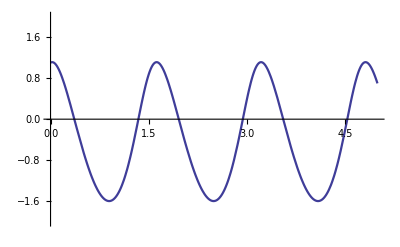

```mathematica
tm=5;coef=4.0 π^2;
xinitial={0,6.5};yinitial={1.1,0.8};
equ={x''[t]==-(coef*x[t])/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-(coef*y[t])/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equ,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
Plot[x[t],{t,0,tm},PlotRange->2,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[y[t],{t,0,tm},PlotRange->2,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[x,y,equ,tm,xinitial,yinitial]
```